前三个能级本征能量：

基态能量E1 = -0.910757 GeV

第一激发态能量E2 = -0.650311 GeV

第二激发态能量E3 = -0.252509 GeV

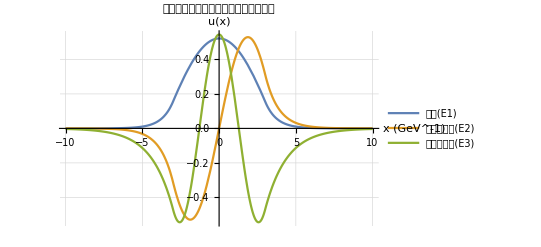

```mathematica
m=1;V0=1;a=3;const=2*m*V0*a^2;
(*定义超越方程（偶宇称）*)
eqEven[x_]:=x*Tan[x]-Sqrt[const-x^2];
(*定义超越方程（奇宇称）*)
eqOdd[x_]:=-x*Cot[x]-Sqrt[const-x^2];
(*基态（偶宇称）*)
x1=FindRoot[eqEven[x],{x,1.2}]//First//Last;
y1=Sqrt[const-x1^2];
(*第一激发态（奇宇称）*)
x2=FindRoot[eqOdd[x],{x,2.5}]//First//Last;
y2=Sqrt[const-x2^2];
(*第二激发态（偶宇称）*)
x3=FindRoot[eqEven[x],{x,4.0}]//First//Last;
y3=Sqrt[const-x3^2];
(*基态参数*)
q1=x1/a;k1=y1/a;E1=-y1^2/(2*m*a^2);
(*第一激发态参数*)
q2=x2/a;k2=y2/a;E2=-y2^2/(2*m*a^2);
(*第二激发态参数*)
q3=x3/a;k3=y3/a;E3=-y3^2/(2*m*a^2);

(*输出前三个能级的本征能量*)
Print["前三个能级本征能量："];
Print["基态能量E1 = ",N[E1]," GeV"];
Print["第一激发态能量E2 = ",N[E2]," GeV"];
Print["第二激发态能量E3 = ",N[E3]," GeV"];

(*基态（偶宇称）归一化系数*)norm1=2*Integrate[Cos[q1*x]^2,{x,0,a}]+2*Integrate[Exp[-2*k1*x],{x,a,∞}]/. Cos[q1*a]->Exp[-k1*a];
A1=1/Sqrt[norm1];
B1=A1*Cos[q1*a]/Exp[-k1*a];

(*第一激发态（奇宇称）归一化系数*)
norm2=2*Integrate[Sin[q2*x]^2,{x,0,a}]+2*Integrate[Exp[-2*k2*x],{x,a,∞}]/. Sin[q2*a]->-Exp[-k2*a];
C2=1/Sqrt[norm2];
D2=-C2*Sin[q2*a]/Exp[-k2*a];

(*第二激发态（偶宇称）归一化系数*)
norm3=2*Integrate[Cos[q3*x]^2,{x,0,a}]+2*Integrate[Exp[-2*k3*x],{x,a,∞}]/. Cos[q3*a]->Exp[-k3*a];
A3=1/Sqrt[norm3];
B3=A3*Cos[q3*a]/Exp[-k3*a];

(*基态波函数（偶宇称）*)u1[x_]:=Piecewise[{{B1*Exp[k1*x],x<-a},{A1*Cos[q1*x],-a<=x<=a},{B1*Exp[-k1*x],x>a}}];

(*第一激发态波函数（奇宇称）*)
u2[x_]:=Piecewise[{{D2*Exp[k2*x],x<-a},{C2*Sin[q2*x],-a<=x<=a},{-D2*Exp[-k2*x],x>a}}];

(*第二激发态波函数（偶宇称）*)
u3[x_]:=Piecewise[{{B3*Exp[k3*x],x<-a},{A3*Cos[q3*x],-a<=x<=a},{B3*Exp[-k3*x],x>a}}];
Plot[{u1[x],u2[x],u3[x]},{x,-10,10},PlotLegends->{"基态(E1)","第一激发态(E2)","第二激发态(E3)"},PlotRange->All,AxesLabel->{"x (GeV^-1)","u(x)"},PlotLabel->"一维有限深势阱前三个能级本征波函数",GridLines->Automatic,BaseStyle->{FontSize->12}]
```